Krishnamoorthy' s case with M, S and G only.  When M=5, S=100, Ga=3, we have thermocapillary instabilities.  Bi has a small value.

```mathematica
Clear[q,Sn,Pm,f,Ga,Bi];
m=5.;Bi=.1;Ga=1;
f=-Ga q^2+(m q^2)/(1+Bi)^2-q^4 Sn
roots=Quiet[Solve[f==0,q]];
{roots[[1]][[1]][[2]],
roots[[2]][[1]][[2]],roots[[3]][[1]][[2]],roots[[4]][[1]][[2]]
}//FullSimplify
```

3.13223 q^2-q^4 Sn

{0.,0.,-1.76981/(√Sn),1.76981/(√Sn)}

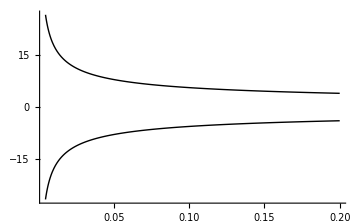

```mathematica
rp=Plot[{roots[[3]][[1]][[2]],
roots[[4]][[1]][[2]]
},{Sn,0,0.2},PlotStyle->{{Thick,Black},{Thick,Black}},PlotPoints->200,PlotRange->{All,Automatic}]
```

3.13223 q^2-1. q^4

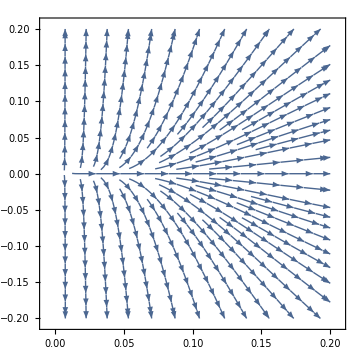

```mathematica
f
pts=Flatten[Table[{q,y},{q,0.,.2,.02},{y,-20,20,4}],1];
vp=VectorPlot[{f,y},{q,0,0.2},{y,-6,6},VectorPoints->{6,4},
VectorStyle->RGBColor[0.9,0.3,0.7],VectorScale->{Large,0.15}];

sp=StreamPlot[{f,y},{q,0,0.2},{y,-.2,.2},PerformanceGoal->"Quality"];
Show[rp,vp];
Show[sp]
```

```mathematica
|
```

```mathematica
Clear[q,Sn,Pm,f,Ga,Bi];
Ga=1;m=5;Sn=100.;Bi=0.;
f=-((Ga q^2)/3)+(m q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
roots=Quiet[Solve[f==0,q]];
{roots[[1]][[1]][[2]],roots[[2]][[1]][[2]],roots[[3]][[1]][[2]],roots[[4]][[1]][[2]]}//FullSimplify
```

{-0.0408248 √(14.-3. Pm-1. √(196.+Pm (-3684.+9. Pm))),0.0408248 √(14.-3. Pm-1. √(196.+Pm (-3684.+9. Pm))),-0.0408248 √(14.-3. Pm+√(196.+Pm (-3684.+9. Pm))),0.0408248 √(14.-3. Pm+√(196.+Pm (-3684.+9. Pm)))}

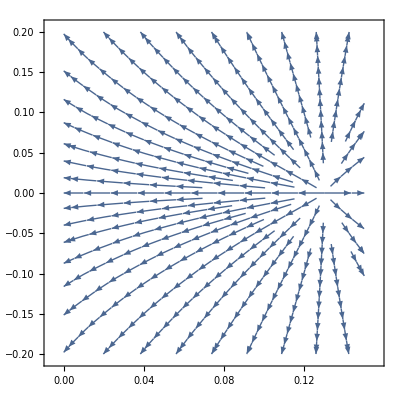

```mathematica
rp=Plot[{roots[[1]][[1]][[2]],roots[[2]][[1]][[2]],roots[[3]][[1]][[2]],
roots[[4]][[1]][[2]]
},{Pm,0,0.2},PlotStyle->{{Thick,Black},{Thick,Black}},PlotPoints->200,PlotRange->{All,Automatic}];

Pm=0.075;
sp=StreamPlot[{-((Ga q^2)/3)+(m q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn,y},{q,-0.0,0.15},{y,-0.2,0.2},PerformanceGoal->"Quality",AspectRatio->1];
Show[sp]
```